NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 10 : Perform the following Line integrals.

1 : Perform the contour integration ∫_C 1/(z-2)ⅆz  
	where C is the upper semicircle with radius 1 centered at point (2, 0) in the anticlockwise sense

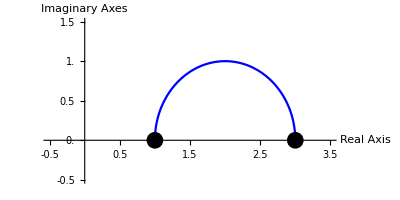

The Value of the contour integration ∫_C 1/(-2+z)ⅆz is ∫_0^π f[z[t]]z'[t]ⅆt = ⅈ π

where C: z[t] = 2+Cos[t]+ⅈ Sin[t], for 0 ≤ t ≤ π.

```mathematica
f[z_] = 1/(z - 2) ; 
z[t_] = (2 + Cos[t]) + ⅈ Sin[t]; 
val = Integrate [f[z[t]] * z '[t], {t, 0, π}]; 
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, 0, π}, PlotRange -> {{-0.5, 3.5}, {-0.5, 1.5}},
Ticks -> {Range[-0.5, 3.5, 0.5], Range[-0.5, 1.5, 0.5]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 

g2 = Graphics[{PointSize[0.03], Point[{3, 0}], Point[{1, 0}]}]; 

Show[g1, g2] 
Print["The Value of the contour integration ", "∫_C ", f[z], "ⅆz is ", "∫_0^π ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for 0 ≤ t ≤ π."];
```

2 : Perform the contour integration ∫_C (2z)/(z^2+2)ⅆz
	where C is the circle z - ⅈ = 1 taken in anticlockwise sense.

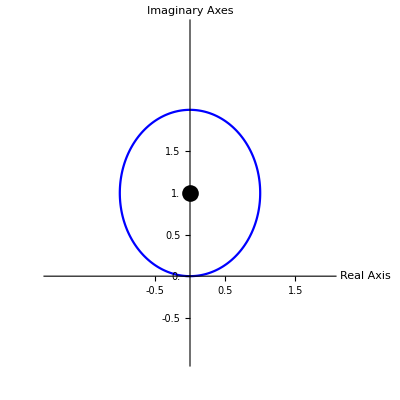

The Value of the contour integration ∫_C (2 z)/(2+z^2)ⅆz is ∫_0^(2  π) f[z[t]]z'[t]ⅆt = 2 ⅈ π

where C: z[t] = Cos[t]+ⅈ (1+Sin[t]), for 0 ≤ t ≤ π.

```mathematica
f[z_] = (2 z)/( z^2 + 2) ; 
z[t_] = Cos[t] + ⅈ (1 + Sin[t]); 
val = Integrate[ f[z[t]] * z '[t], {t, 0, 2 π}]; 
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, 0, 2π}, PlotRange -> {{-2,2}, {-1, 3}},
Ticks -> {Range[-0.5, 3.5, 0.5], Range[-0.5, 1.5, 0.5]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 

g2 = Graphics[{PointSize[0.03], Point[{0, 1}]}]; 

Show[g1, g2] 
Print["The Value of the contour integration ", "∫_C ", f[z], "ⅆz is ", "∫_0^(2  π) ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for 0 ≤ t ≤ π."];
```

3 : Perform the contour integration ∫_C 1/z ⅆz
	where C is the circle z = 1 taken in clockwise sense.

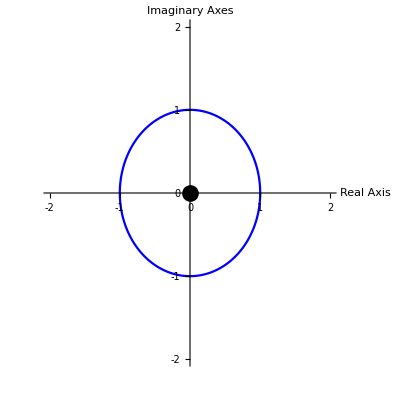

The Value of the contour integration ∫_C 1/z ⅆz is ∫_0^π  f[z[t]]z'[t]ⅆt = -2 ⅈ π

where C: z[t] = ⅈ Cos[t]+Sin[t], for 0 ≤ t ≤ π.

```mathematica
ClearAll;
f[z_] = 1/z ; 
z[t_] = Sin[t] + ⅈ Cos[t]; 
val = Integrate[ f[z[t]]*z'[t], {t, 0, 2 π}];
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, 0, 2 π}, PlotRange -> {{-2,2}, {-2,2}},
Ticks -> {Range[-2,2,1], Range[-2,2,1]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 

g2 = Graphics[{PointSize[0.03], Point[{0, 0}]}]; 

Show[g1, g2] 
Print["The Value of the contour integration ", "∫_C ", f[z], "ⅆz is ", "∫_0^π  ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for 0 ≤ t ≤ π."];
```

4 : Perform the contour integration ∫_C z^3+2 z^2+1ⅆz
	where C is the contour given by x2 + y2 = 1 taken in the positive sense.

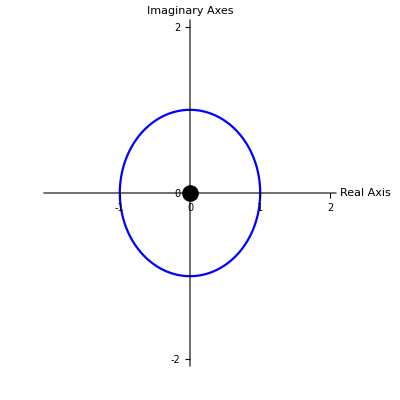

The Value of the contour integration ∫_C 1+2 z^2+z^3ⅆz is ∫_0^(2  π)  f[z[t]]z'[t]ⅆt = 0

where C: z[t] = Cos[t]+ⅈ Sin[t], for 0 ≤ t ≤ π.

```mathematica
f[z_] = z^3 + 2 z^2 + 1; 
z[t_] = Cos[t] + ⅈ Sin[t]; 
val = Integrate[f[z[t]] * z '[t], {t,0,2 π}];
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, 0, 2 π}, PlotRange -> {{-2, 2}, {-2, 2}},
Ticks -> {Range[-1, 2, 1], Range[-2, 2, 2]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 

g2 = Graphics[{PointSize[0.03], Point[{0, 0}]}]; 

Show[g1, g2] 
Print["The Value of the contour integration ", "∫_C ", f[z], "ⅆz is ", "∫_0^(2  π)  ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for 0 ≤ t ≤ π."];
```